## Eigenvalue Analysis of Finite Temperature TFD Hamiltonian

We will study TFD Hamiltonian at finite temperature. We will use the following form of the TFD Hamiltonian:
  H = ⅇ^(-β/4(H_L + H_R))  (O × 1 - 1 × O^T)  ⅇ^(β/4(H_L + H_R))

Does our ground state really stay in the symmetric subspace? 
What is the overlap of our state with the original TFD state?

## Common Parameters

```mathematica
Quit[];
```

```mathematica
Δ=1/2;
kmax=1;
Nbig=11;
nstep=5;
neff=0.4;    (* This value tells the effective width of the band. It should be chosen properly. *)
sigma=1/Sqrt[neff];  (* It is not very clear to me what is the use of this sigma parameter *)
β =1/3;         (* the real temperature of the TFD state *)
δ=1;            (* the unit of measurement of energy *)
```

```mathematica
energy[i_]:=δ(1+ProductLog[g i ])^(1/p); 
g=1/3;
p=0.6;
```

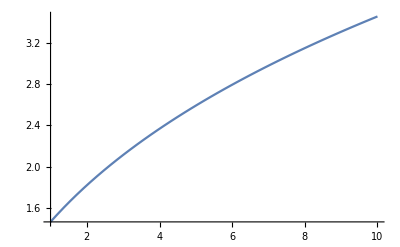

```mathematica
Plot[energy[x],{x,1,10}, PlotRange -> All]
```

Just for future reference, we note that ΔEmax and ΔE for us is

```mathematica
N[energy[Nbig]]
N[energy[1]]
N[energy[Nbig]]-N[energy[Nbig-nstep]]
```

6.56985

1.46528

0.243951

```mathematica
avgEnergy=Table[
estar[i_]=N[(energy[i]+energy[1])/2],
{i,1,Nbig,nstep}];
avgQnumber=Table[
istar[i_]=N[(ⅇ^(-1+(ee/δ)^p) (-1+(ee/δ)^p))/g/.{ee -> estar[i]}],
{i,1,Nbig,nstep}];
```

## Consistency check for β(E) and S(E)

```mathematica
Solve[(ee/δ)^p-1==ProductLog[ i g],i]
```

{{i→(ⅇ^(-1+(ee/δ)^p) (-1+(ee/δ)^p))/g}}

```mathematica
D[(ⅇ^(-1+(ee/δ)^p) (-1+(ee/δ)^p))/g,ee]//FullSimplify
```

(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)

```mathematica
di/(d(ee))==(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)(* density of states rho(E) *)
```

```mathematica
Log[(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)]  (* entropy(E) *)
```

Log[(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)]

```mathematica
D[Log[(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)],ee]//FullSimplify   (* beta(E) *)
```

(-1+p (2+(ee/δ)^p))/ee

```mathematica
D[(-1+p (2+(ee/δ)^p))/ee,ee]//FullSimplify    (*  S''(E)  *)
```

(1-2 p+(-1+p) p (ee/δ)^p)/ee^2

```mathematica
rho[ee_]:=(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)
entropy[ee_]:=Log[(ⅇ^(-1+(ee/δ)^p) p (ee/δ)^(2 p))/(ee g)]
beta[ee_]:=(-1+p (2+(ee/δ)^p))/ee
Spp[ee_]:=(1-2 p+(-1+p) p (ee/δ)^p)/ee^2
```

```mathematica
entropy[x]//FullSimplify
beta[x]//FullSimplify
Spp[x]//FullSimplify
```

Log[0.662183 ⅇ^(x^0.6) x^0.2]

(0.2+0.6 x^0.6)/x

(-0.2-0.24 x^0.6)/x^2

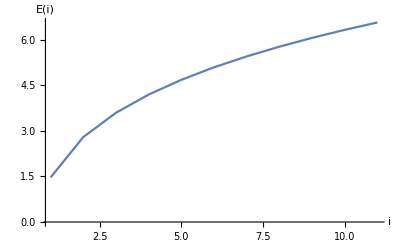

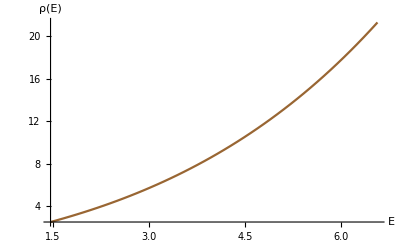

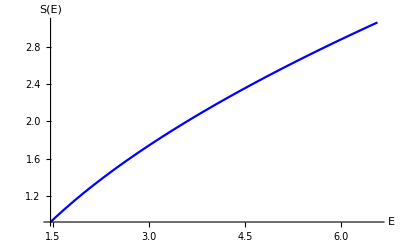

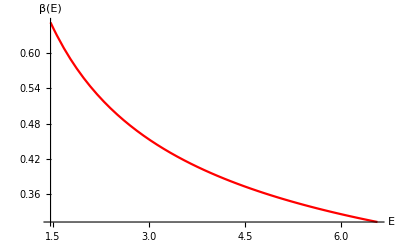

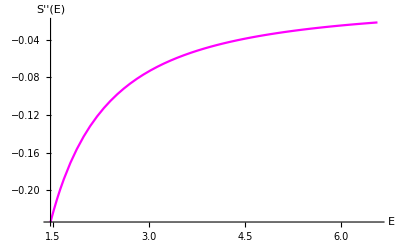

18.5215

```mathematica
enetab=Table[energy[i],{i,1,Nbig,nstep}];
ListLinePlot[enetab, PlotRange->All, AxesLabel->{"i","E(i)"}]
Plot[rho[x],{x,energy[1],energy[Nbig]},PlotRange->All, PlotStyle->Brown, AxesLabel->{"E","ρ(E)"}]
Plot[entropy[x],{x,energy[1],energy[Nbig]},PlotRange->All, PlotStyle->Blue, AxesLabel->{"E","S(E)"}]
Plot[beta[x],{x,energy[1],energy[Nbig]},PlotRange->All, PlotStyle->Red, AxesLabel->{"E","β(E)"}]
Plot[Spp[x],{x,energy[1],energy[Nbig]},PlotRange->All, PlotStyle->Magenta, AxesLabel->{"E","S''(E)"}]
N[4/(√(-Spp[x]))]/.{x -> estar[Nbig]}
```

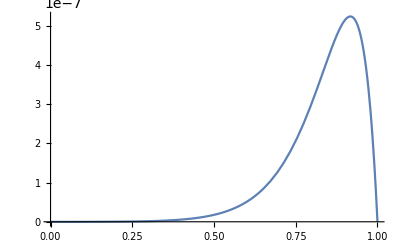

```mathematica
Clear[p]
tempf[p_]:=Evaluate[-Spp[x]/.{x -> estar[Nbig]}//Simplify]
p=0.1;
Plot[tempf[p],{p,0,1}]
```

```mathematica
N[(energy[Nbig]-estar[Nbig])^(1/p)/(4 Spp[estar[Nbig]])]
N[(energy[1]-estar[Nbig])^(1/p)/(4 Spp[estar[Nbig]])]
```

-1.98322×10^7

9.91608×10^6+1.71752×10^7 ⅈ

The following number comes in the exponent of the wavefunction Exp[- #]

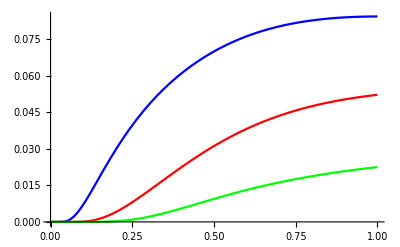

```mathematica
Plot[{(energy[Nbig]-(estar[Nbig]))^(1/p)/(16 (estar[Nbig])^(1+1/p))/.{g -> 1/20}, (energy[Nbig]-(estar[Nbig]))^(1/p)/(16 (estar[Nbig])^(1+1/p))/.{g -> 1/7},(energy[Nbig]-(estar[Nbig]))^(1/p)/(16 (estar[Nbig])^(1+1/p))/.{g -> 1}},{p,0,1}, PlotRange->All, PlotStyle->{Blue, Red, Green}]
```

These graphs indicate that we are in the good regime at relatively high temperatures, where the energy spectrum we have is a good model for holographic spectra.

```mathematica
N[∫_1^40 rho[x] ⅆx] (* Δi required *)
```

76.6225

## How did we find the parameters β , δ and istar(Nbig) ?

We fix p=1/2 . We demand that β(E) is equal to β at E_*(N). We also demand that E_* corresponds to i_*(N)

```mathematica
NSolve[beta[ee]==1/3,ee]
N[estar[Nbig]]
```

{{ee→5.73122}}

4.01757

```mathematica
NSolve[(-1+p (2+(estar[Nbig]/delta)^p))/estar[Nbig]==1/3,delta]
```

{{delta→1.38003}}

```mathematica
NSolve[δ(1+ProductLog[is g])^(1/p)==estar[Nbig],is]
istar[Nbig]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{is→14.3977}}

14.3977

Thus we have ensured that the mean energy around which our energy window is centered does occur in the numerical energies the computer can deal with.

## Defining the TFD Hamiltonian

```mathematica
Table[
ExpHij1[nm_]:=Table[ⅇ^(β/4 energy[i])  KroneckerDelta[i,j],{i,1,nm},{j,1,nm}];
ExpHij2[nm_]:=Table[ⅇ^(-β/4 energy[i])  KroneckerDelta[i,j],{i,1,nm},{j,1,nm}];
ExpHij3[nm_]:=Table[ⅇ^(-β/2 energy[i])  KroneckerDelta[i,j],{i,1,nm},{j,1,nm}];
Rij[nm_]:=Chop[Table[ⅇ^(-(energy[i]-energy[j])^2/(2 neff^2))* RandomVariate[NormalDistribution[0,1]],{i,nm},{j,nm}],10^-5];
Oij[nm]=Table[Rij[nm],{k,1,kmax}];
Hamk[nm]=Table[ 
KroneckerProduct[ExpHij1[nm].Transpose[Oij[nm][[k]]].ExpHij3[nm].Oij[nm][[k]].ExpHij1[nm], IdentityMatrix[nm]] - KroneckerProduct[ExpHij1[nm].Transpose[Oij[nm][[k]]].ExpHij2[nm],ExpHij2[nm].Transpose[Oij[nm][[k]]].ExpHij1[nm]] - KroneckerProduct[ExpHij2[nm].Oij[nm][[k]].ExpHij1[nm],ExpHij1[nm]. Oij[nm][[k]].ExpHij2[nm]] + KroneckerProduct[IdentityMatrix[nm], ExpHij1[nm].Oij[nm][[k]].ExpHij3[nm].Transpose[Oij[nm][[k]]].ExpHij1[nm]] 
,{k,1,kmax}];
TFDHam[nm]=Chop[1/kmax Sum[Hamk[nm][[k]],{k,1,kmax}],10^-5];
,{nm,1,Nbig,nstep}];
```

```mathematica
Share[];
```

## Matrixplots of the TFD Hamiltonian

```mathematica
tfdmatplotRS=MatrixPlot[TFDHam[Nbig], PlotLabel->"(51)^2x(51)^2 HTFD.Red=0+,Blue=0-,White=0.β=1/3,n_eff=0.4,K=20"]
```

-Graphics-

## Ground state in the energy space

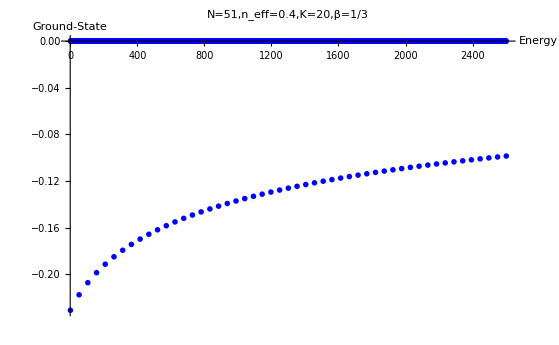

```mathematica
gsplotRS=ListPlot[Eigenvectors[TFDHam[Nbig]][[-1]],AxesLabel->{"Energy", "Ground-State"},  PlotRange->All, PlotMarkers->{Automatic, Tiny}, PlotStyle->Blue,  PlotLabel->"N=51,n_eff=0.4,K=20,β=1/3"]
```

## Is the ground state in the symmetric subspace?

The following are the orthonormal basis vectors for the symmetric subspace.

```mathematica
Table[
tempvec[i]=Table[KroneckerDelta[i,j],{j,1,Nbig}];
vec[i]=Flatten[ KroneckerProduct[ tempvec[i] ,tempvec[i]   ] ];
,{i,1,Nbig}];
```

The projection matrix to project on the symmetric subspace can be found as follows

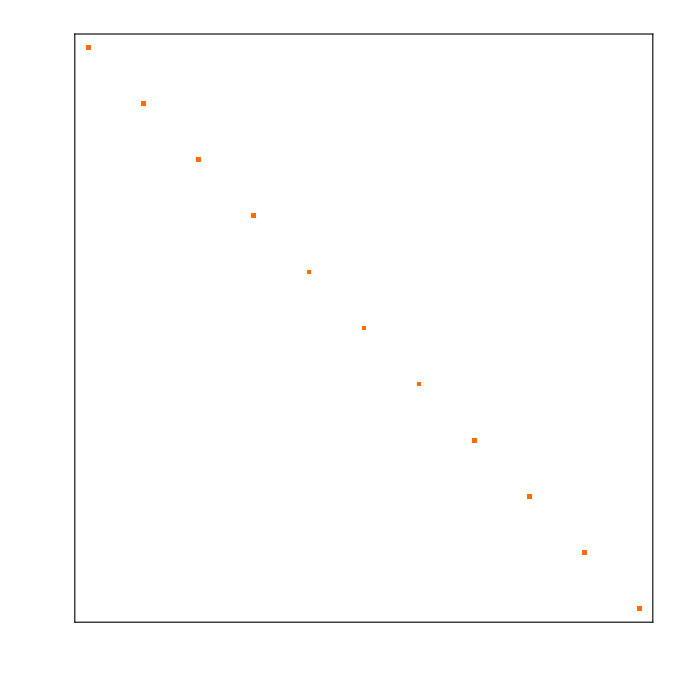

```mathematica
atemp=Transpose[Table[vec[i],{i,1,Nbig}]];
proj=atemp.Transpose[atemp];
MatrixPlot[proj,PlotTheme->"MinimalAxes" ]
```

```mathematica
Length[vec[1]]
Dimensions[proj]
```

2601

{2601,2601}

Is this really the projection matrix? Yes, because

```mathematica
Norm[proj.Flatten[KroneckerProduct[tempvec[4],tempvec[5]]]]
```

0

121

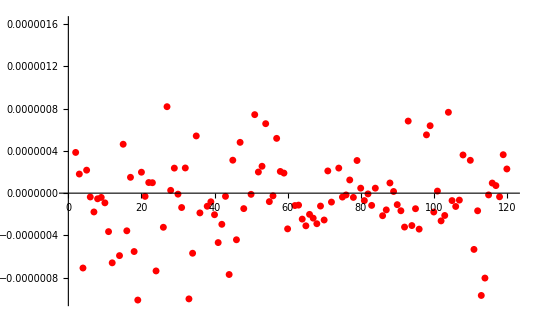

```mathematica
gstate=Eigenvectors[TFDHam[Nbig]][[-1]];
Length[gstate]
ListPlot[gstate,PlotStyle->Red]
```

```mathematica
$MaxExtraPrecision=50
```

50

```mathematica
gstate
```

{0.365524,3.8492×10^-7,1.80591×10^-7,-7.07563×10^-7,2.17294×10^-7,-3.62767×10^-8,-1.77672×10^-7,-5.33535×10^-8,-4.0259×10^-8,-9.1479×10^-8,-3.63607×10^-7,-6.58442×10^-7,0.344512,-5.90361×10^-7,4.62286×10^-7,-3.55868×10^-7,1.49681×10^-7,-5.51734×10^-7,-1.01036×10^-6,1.97966×10^-7,-3.0343×10^-8,1.00369×10^-7,9.8652×10^-8,-7.35094×10^-7,0.328044,-3.22538×10^-7,8.17128×10^-7,2.64755×10^-8,2.36549×10^-7,-9.58569×10^-9,-1.35872×10^-7,2.38013×10^-7,-9.99352×10^-7,-5.67869×10^-7,5.40733×10^-7,-1.86549×10^-7,0.314474,-1.23755×10^-7,-8.16412×10^-8,-2.03834×10^-7,-4.67216×10^-7,-2.94401×10^-7,-3.00188×10^-8,-7.68961×10^-7,3.11417×10^-7,-4.4055×10^-7,4.80195×10^-7,-1.46137×10^-7,0.30293,-1.12037×10^-8,7.42017×10^-7,1.99822×10^-7,2.54181×10^-7,6.56578×10^-7,-8.01221×10^-8,-2.5266×10^-8,5.17758×10^-7,2.05066×10^-7,1.8955×10^-7,-3.37507×10^-7,0.292889,-1.17127×10^-7,-1.13048×10^-7,-2.45382×10^-7,-3.08717×10^-7,-2.00568×10^-7,-2.3618×10^-7,-2.8881×10^-7,-1.21927×10^-7,-2.53799×10^-7,2.10012×10^-7,-8.44259×10^-8,0.284011,2.36937×10^-7,-3.71186×10^-8,-1.69175×10^-8,1.24562×10^-7,-4.01103×10^-8,3.08473×10^-7,4.71628×10^-8,-7.02783×10^-8,-7.09448×10^-9,-1.15643×10^-7,4.72258×10^-8,0.276061,-2.13179×10^-7,-1.58106×10^-7,9.62057×10^-8,1.5811×10^-8,-1.0874×10^-7,-1.66392×10^-7,-3.20555×10^-7,6.81216×10^-7,-3.06286×10^-7,-1.47053×10^-7,-3.3999×10^-7,0.268868,5.50937×10^-7,6.37225×10^-7,-1.78216×10^-7,1.96329×10^-8,-2.62045×10^-7,-2.10995×10^-7,7.64307×10^-7,-7.03063×10^-8,-1.25859×10^-7,-6.57368×10^-8,3.60839×10^-7,0.262307,3.10402×10^-7,-5.31695×10^-7,-1.66777×10^-7,-9.66921×10^-7,-8.02602×10^-7,-1.67122×10^-8,9.55349×10^-8,7.13153×10^-8,-3.43767×10^-8,3.6333×10^-7,2.28581×10^-7,0.256279}

MachinePrecision[1.]

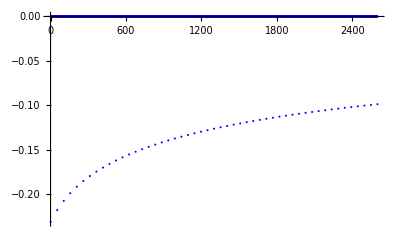

```mathematica
gsproj=proj.gstate;
MachinePrecision[Norm[gsproj]]
ListPlot[gsproj,PlotStyle->Blue]
```

0.569553

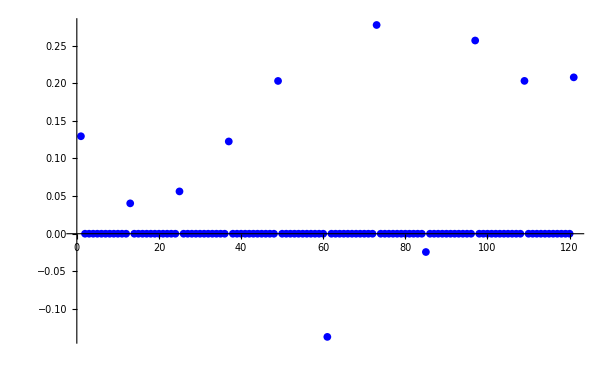

```mathematica
esproj=proj.Eigenvectors[TFDHam[Nbig]][[-2]];
Norm[esproj]
ListPlot[esproj,PlotStyle->Blue]
```

## First excited state in the energy space

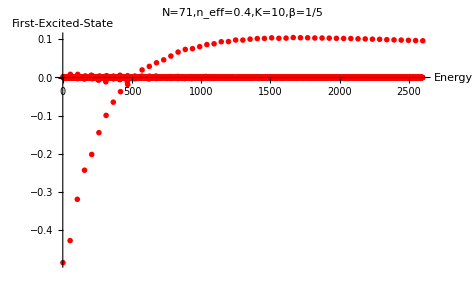

```mathematica
esplotRS=ListPlot[Eigenvectors[TFDHam[Nbig]][[-2]],AxesLabel->{"Energy", "First-Excited-State"},  PlotRange->All, PlotMarkers->{Automatic, Tiny}, PlotStyle->Red,  PlotLabel->"N=71,n_eff=0.4,K=10,β=1/5"]
```

```mathematica
gsproj=proj.gstate
```

## Plots of the Gap

```mathematica
Gap=Table[{i,Eigenvalues[TFDHam[i]][[-2]]},{i,1,Nbig,nstep}];
```

Part::partw: Part -2 of {0} does not exist.

```mathematica
Share[];
```

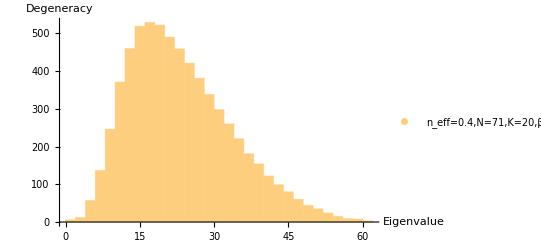

```mathematica
histoRS=Histogram[Eigenvalues[TFDHam[Nbig]],20, AxesLabel->{"Eigenvalue","Degeneracy"}, ChartLegends->Placed[PointLegend[{"n_eff=0.4,N=71,K=20,β=1/5"},LegendFunction->(Framed[#, RoundingRadius -> 4] &) ] ,Above]]
```

```mathematica
Gap
```

{{1,{0}⟦-2⟧},{6,0.683017},{11,0.362033},{16,0.263525},{21,0.224392},{26,0.208007},{31,0.185106},{36,0.163757},{41,0.153905},{46,0.144698},{51,0.132931}}

Part::partw: Part -2 of {0.} does not exist.

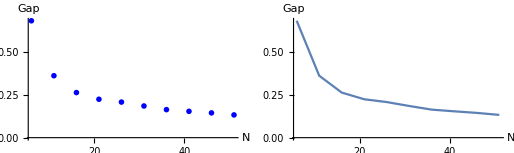

```mathematica
temp5=ListPlot[Gap,AxesLabel->{"N", "Gap"},  PlotRange->All,PlotStyle->Blue, PlotMarkers->{Automatic, Tiny}];
temp6=ListLinePlot[Gap,AxesLabel->{"N", "Gap"},  PlotRange->All];
GapPlotRS=GraphicsRow[{temp5,temp6}, PlotLabel->"N=71,n_eff=0.4,K=10,β=1/5"]
```

## What functions should we use for S' and S'' ?

Definitions for every energy using the analytic functions (for a fixed N)

```mathematica
Table[
betaTable[nm]=Table[beta[energy[i]],
{i,1,nm}];
SppTable[nm]=Table[Spp[energy[i]],
{i,1,nm}];
,{nm,1,Nbig,nstep}];
```

Following are the definitions we get by using discrete derivatives

```mathematica
Table[
tempS[nm]=Table[entropy[energy[i]],{i,1,nm}];
tempSprime[nm]= Flatten[{1,Table[tempS[nm][[i]]-tempS[nm][[i-1]],{i,2,nm}]}];
,{nm,1,Nbig,nstep}];
Table[tempSdoubleprime[nm]=Flatten[{1,Table[tempS[nm][[i+1]]-2 tempS[nm][[i]]+tempS[nm][[i-1]],{i,2,nm-1}],1}];
,{nm,1+nstep,Nbig,nstep}];
tempSdoubleprime[1]={1.};
```

Let us plot the two S'  functions below:

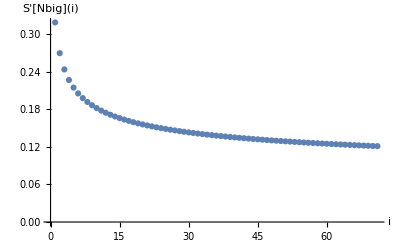

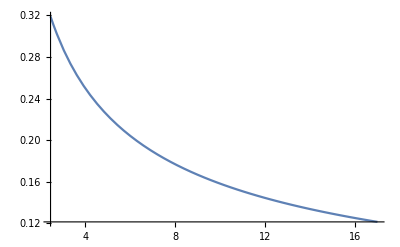

```mathematica
ListPlot[betaTable[Nbig],PlotRange->All, AxesLabel->{"i","S'[Nbig](i)"}]
Plot[beta[x],{x,energy[1],energy[Nbig]}]
```

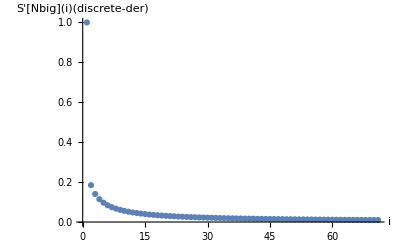

```mathematica
ListPlot[tempSprime[Nbig],PlotRange->All,AxesLabel->{"i","S'[Nbig](i)(discrete-der)"}]
```

Let us also plot the second derivatives of entropy:

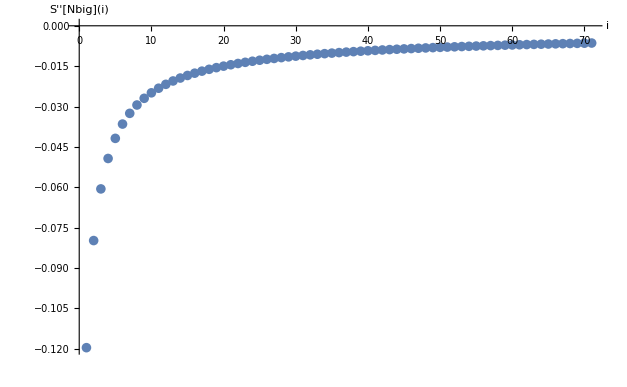

```mathematica
bb=ListPlot[SppTable[Nbig],PlotRange->All,AxesLabel-> {"i","S''[Nbig](i)"}]
```

```mathematica
N[SppTable[Nbig][[18]]]
```

-0.0161749

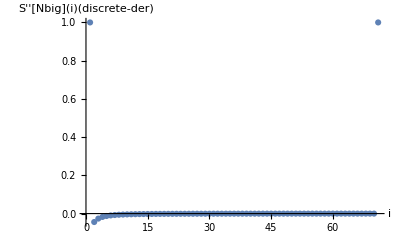

```mathematica
ListPlot[tempSdoubleprime[Nbig],PlotRange->All,AxesLabel->{"i","S''[Nbig](i)(discrete-der)"}]
```

Clearly the functions with discrete derivatives are bad. Henceforth we will use Saprime1 and Sadp1 for S' and S'' resp.

## The functions h and g

```mathematica
(* We need to calculate the function h *)
```

```mathematica
Table[
hfunc[nm]=Table[ Sqrt[∑_(j=1)^nm  ∑_(k=1)^kmax 1/kmax  1/2 (energy[j]-energy[i])^2 ((Oij[nm][[k]][[j,i]])^2 + (Oij[nm][[k]][[i,j]])^2) (rho[estar[nm]]/rho[energy[j]])],{i,1,nm}];
gfunc[nm]=Table[ ∑_(j=1)^nm (energy[j]-energy[i])  1/kmax∑_(k=1)^kmax ((Oij[nm][[k]][[j,i]])^2 + (Oij[nm][[k]][[i,j]])^2) (rho[estar[nm]]/rho[energy[j]]),{i,1,nm}];
avghsq[nm]= ∑_(i=1)^nm 1/nm hfunc[nm][[i]]*hfunc[nm][[i]];
,{nm,1,Nbig,nstep}];
```

## Plots of the analytic functions

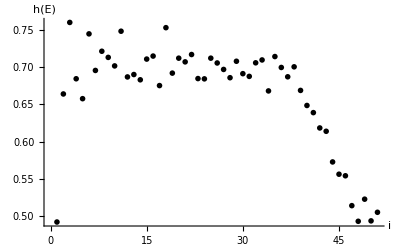

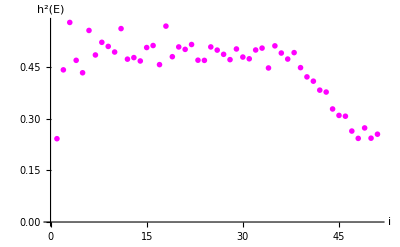

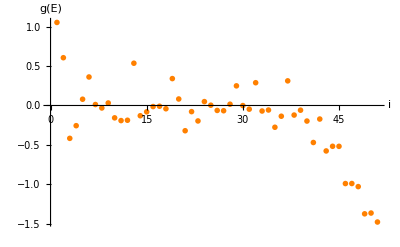

```mathematica
htemp9=ListPlot[hfunc[Nbig], AxesLabel->{"i","h(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny}, PlotStyle->Black];
hplotRS=GraphicsRow[{htemp9},PlotLabel-> "N=71,n_eff=0.4,K=10,β=1/5"]


hsqtemp9=ListPlot[hfunc[Nbig]*hfunc[Nbig], AxesLabel->{"i","h^2(E)"}, PlotRange -> All,PlotMarkers->{Automatic,Tiny}, PlotStyle->Magenta];
hsqplotRS=GraphicsRow[{hsqtemp9},PlotLabel-> "N=71,n_eff=0.4,K=10,β=1/5"]


gtemp9=ListPlot[gfunc[Nbig], AxesLabel->{"i","g(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny},PlotStyle->Orange];
gplotRS=GraphicsRow[{gtemp9},PlotLabel->"N=71,n_eff=0.4,K=10,β=1/5"]
```

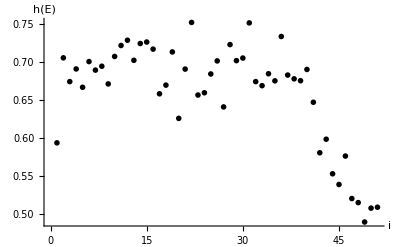

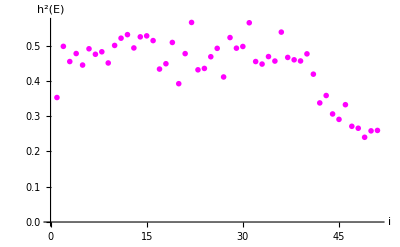

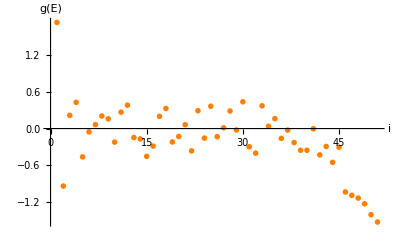

## Final analytic expression for gap GAP= - h^2(E_*) S''(E_*)

The numerical gap is

```mathematica
Gap
```

{{1,{0}⟦-2⟧},{6,0.591033},{11,0.366327},{16,0.281931},{21,0.219334},{26,0.186113},{31,0.177363},{36,0.164226},{41,0.15632},{46,0.151246},{51,0.137373},{56,0.124732},{61,0.126668},{66,0.120417},{71,0.116254},{76,0.114795},{81,0.113857}}

```mathematica
fingap=-hfunc[Nbig][[Floor[istar[Nbig]]]]*hfunc[Nbig][[Floor[istar[Nbig]]]]*Spp[estar[Nbig]]
```

0.0225821

## The full expression for the Partner Potential

## Definition of h'

```mathematica
Table[
hprime[nm]=Flatten[{0.01,Table[hfunc[nm][[i]]-hfunc[nm][[i-1]],{i,2,nm}]}];
,{nm,1,Nbig,nstep}];
Table[
hdoubleprime[nm]=Flatten[{0.01,Table[hfunc[nm][[i+1]]-2 hfunc[nm][[i]]+hfunc[nm][[i-1]],{i,2,nm-1}],0.001}];
,{nm,1+nstep,Nbig,nstep}];
hdoubleprime[1]={0.01};
```

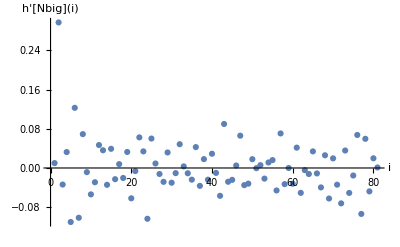

```mathematica
cc=ListPlot[hprime[Nbig],PlotRange->All,AxesLabel->{"i","h'[Nbig](i)"}]
```

## Relation between the functions g and h

```mathematica
(* g(E)=?= 2 h(E) hprime(E) with the new definitions *)
```

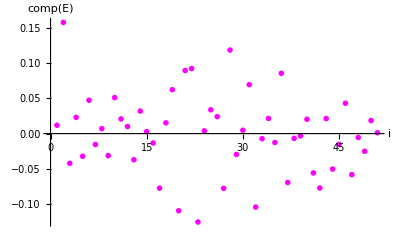

```mathematica
Table[
comp[nm]=Table[2 hfunc[nm][[i]]*hprime[nm][[i]],{i,1,nm}];
,{nm,1,Nbig,nstep}];
dd=ListPlot[comp[Nbig], AxesLabel->{"i","comp(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny},PlotStyle->Magenta]
```

```mathematica
ListPlot[gfunc[Nbig], AxesLabel->{"i","g(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny}, PlotStyle->Orange]
```

-Graphics-

## Comparison with Analytic Gap

```mathematica
(* The gap is given by the minimum of the potential V=1/4 h'[E]^2 + h^2/4 (1/T[E]-β)-1/2 h h''[E]-1/2 h^2 S''[E] *)
```

```mathematica
(* -1/2 hfunc[nm]* hdoubleprime[nm] *)
```

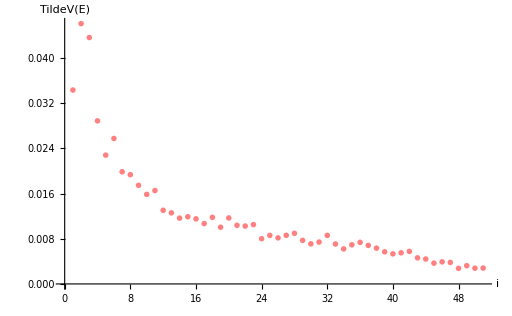

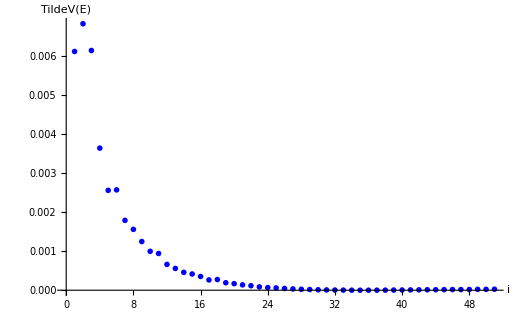

```mathematica
Table[Vtilde[nm]= hfunc[nm]^2/4(betaTable[nm]-β)^2-1/2 hfunc[nm]^2 * SppTable[nm]+1/4 hprime[nm]^2 ,{nm,1,Nbig,nstep}];
ff=ListPlot[Vtilde[Nbig], AxesLabel->{"i","TildeV(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny},PlotStyle-> Pink]
ListPlot[hfunc[Nbig]^2/4(betaTable[Nbig]-β)^2, AxesLabel->{"i","TildeV(E)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny},PlotStyle-> Blue]
```

```mathematica
Min[Abs[Vtilde[Nbig]]]
```

0.000479222

```mathematica
Gap
```

{{1,{0}⟦-2⟧},{6,0.683017},{11,0.362033},{16,0.263525},{21,0.224392},{26,0.208007},{31,0.185106},{36,0.163757},{41,0.153905},{46,0.144698},{51,0.132931}}

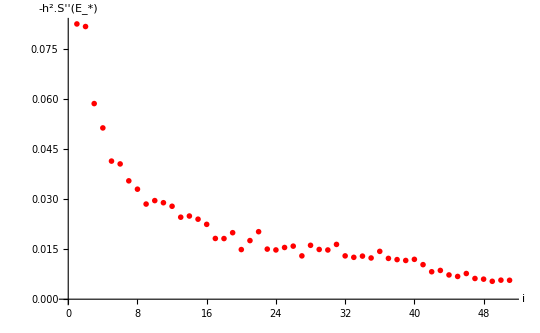

```mathematica
Table[newgap[nm]= - hfunc[nm]*hfunc[nm]*SppTable[nm];
,{nm,1,Nbig,nstep}];
nn=ListPlot[newgap[Nbig], AxesLabel->{"i","-h^2.S''(E_*)"},PlotRange -> All, PlotMarkers->{Automatic,Tiny}, PlotStyle->Red]
```

Part::partw: Part -2 of {0.} does not exist.

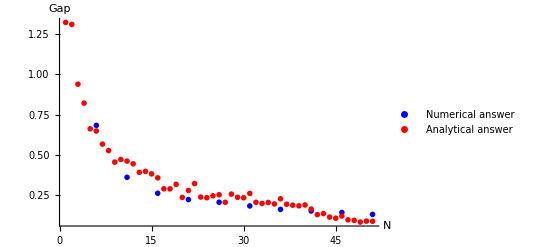

```mathematica
temp001=ListPlot[Gap,  PlotRange->All, PlotMarkers->{Automatic, Tiny},PlotStyle->Blue, PlotLegends->{"Numerical answer"}];
temp002=ListPlot[16 newgap[Nbig],PlotRange -> All, PlotMarkers->{Automatic,Tiny}, PlotStyle->Red, PlotLegends->{"Analytical answer"}];
mm=Show[temp001,temp002, PlotRange -> All,AxesLabel -> {"N","Gap"}]
```

Part::partw: Part -2 of {0.} does not exist.

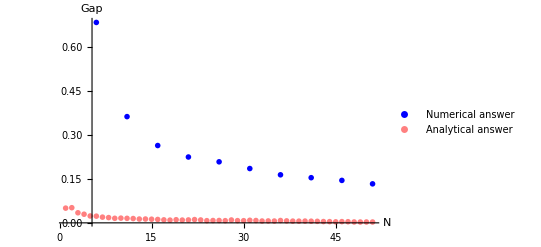

```mathematica
temp003=ListPlot[Gap,  PlotRange->All, PlotMarkers->{Automatic, Tiny},PlotStyle->Blue, PlotLegends->{"Numerical answer"}];
temp004=ListPlot[Vtilde[Nbig],PlotRange -> All, PlotMarkers->{Automatic,Tiny},PlotStyle-> Pink, PlotLegends->{"Analytical answer"}];
qq=Show[temp003,temp004, PlotRange -> All,AxesLabel -> {"N","Gap"}]
```

```mathematica
newgap[Nbig][[18]]
```

0.00156903

Analytic upper bound on the gap

```mathematica
avghsq[Nbig]
```

0.427644

```mathematica
gapexpres=Table[{i,((2 π)^2  avghsq[i])/i^2},{i,1,Nbig,nstep}]
```

{{1,0.},{6,0.448107},{11,0.130713},{16,0.0616228},{21,0.0383268},{26,0.0259947},{31,0.0188403},{36,0.0137293},{41,0.0104374},{46,0.00821352},{51,0.00667787}}

Part::partw: Part -2 of {0.} does not exist.

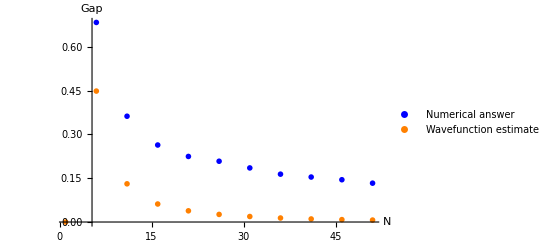

```mathematica
temp12=ListPlot[Gap,  PlotRange->All, PlotMarkers->{Automatic, Tiny},PlotStyle->Blue, PlotLegends->{"Numerical answer"}];
temp13=ListPlot[gapexpres,PlotRange -> All, PlotMarkers->{Automatic,Tiny}, PlotStyle->Orange, PlotLegends->{"Wavefunction estimate"}];
kk=Show[temp12,temp13, PlotRange -> All,AxesLabel -> {"N","Gap"}]
```